# Quantica

## Calculator of quantum systems with mathematica

21 December, 2013

## Time domain problem

### Kicked rotator

ハミルトニアン

H(q,p,t) = T(p) + V(q)∑_(n∈ℤ) δ(t-n)

で定義される時間発展演算子(量子写像Qmapと呼ぶ事にする)

U(t+1,t)=exp[-i/ℏT(p)]exp[-i/ℏV(p)]

による状態の時間発展について考える

T(p)=p^2/2,    V(q)=k/(4 π^2)Cos(2πq)

を考える.

```mathematica
Exit[];
```

```mathematica
Get["Quantica`"];
dps=20;
Quantica`MP`dps=dps;
k=1;
T[x_]:=x^2/2
V[x_]:=k*Cos[2*Pi*x]/(4*Pi*Pi)
dim=70;
domain={{0,1},{-2,2}};
QuanticaSetting[dim,domain,Verbose->True]
SetSystem[T,V];
tmax = 7;
pvec = State`Unit[dim/2+1];
qvec = State`P2Q[pvec];
```

{Dim:,70,Domain:,{{0,1},{-2,2}},Tau:,1,dps:,20}

```mathematica
qrepdata = NestList[ Qmap`Evolve,  qvec, tmax];
prepdata = Map[State`Q2P, qrepdata];
```

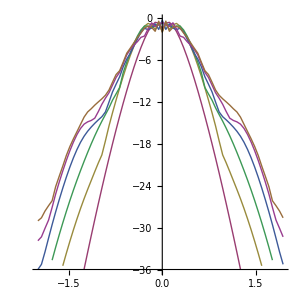

```mathematica
data[n_] := Table[  {  X[[2]][[i]],Log10[State`Abs2[  prepdata[[n]][[i]] ]]},{i,1,dim}];
datalist=Map[data,Range[tmax]];
ListPlot[ datalist,
Joined->True,PlotRange->All,ImageSize->{300,300},AspectRatio->1]
```

## Related Links

Notes on Scientific Computing with Python